```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/26/2010     *)
```

```mathematica
(*  Assignment #4 *)
```

```mathematica
(* Problem #3   *)
```

```mathematica
(*  part A:
Utilize a change in variables to create a homogeneous BVP that we have solved previously.  Allow T(x,t)= to be composed of a steady state term and a transient term, such that:
T(x,t)=Ts(x)+Tt(x,t)   

Using this substitution we can write a differential equation for each of the components of T(x,t):

(∂Ts(x))/dt=D(∂^2 Ts(x))/(∂^2 x) (Eq.1) and (∂Ts(x))/dt+(∂Tt(x,t))/dt=D(∂^2 Ts(x))/(∂^2 x)+D(∂^2 Tt(x,t))/(∂^2 x) (Eq 2)

Note: (∂Ts(x))/dx=(∂^2 Ts(x))/(∂^2 x)=0.  Therfore, Eq. 1 and 2 simplify to:
G=D(∂^2 Ts(x))/(∂^2 x)   (Eq. 3)   and (∂Tt(x,t))/dt=D(∂^2 Tt(x,t))/(∂^2 x)    (Eq. 4)
These equations have Boundary Conditions:
Ts(0)=0, Ts(L)=T1, Tt(0,t)=0, Tt(L,t)=0, and Tt(x,0)=f(x)-Ts(x),
where f(x) is known.   *)
```

```mathematica
(* Part B:  Solving Steady State part *)
```

```mathematica
(* equation 3 is solved simply by integrating both sides of the equation with respect to x to yield:
Ts[x]=G/(2D)x^2+Ax+B.  The Boundary Conditions tell us that:   *)
```

```mathematica
Clear[g,d,L,A,B]
```

```mathematica
Ts[x_]=-g/(2d)x^2+A*x+B
```

B+A x-(g x^2)/(2 d)

```mathematica
Clear[A,B]
```

```mathematica
Solve[{Ts[0]==0},{B}]
```

{{B→0}}

```mathematica
Solve[{Ts[l]==0},{A}]
```

{{A→(-2 B d+g l^2)/(2 d l)}}

```mathematica
B=0;
A=(-2 B d+G l^2)/(2 d l)
```

(G l)/(2 d)

```mathematica
Clear[d,g,l,T0,T1]
```

```mathematica
Ts[x]=((g L^2)/(2d))x^2+(T1-(g*L)/(2d))x
```

(-(g L)/(2 d)+T1) x+(g L^2 x^2)/(2 d)

```mathematica
(* Part B : Determination of the Transient part of T[x,t]
 *)
```

```mathematica
SetAttributes[{L,g,T0,T1,d},Constant];
Clear[T0]
f[x_]:=T0;
```

```mathematica
Ts[x]=((g L^2)/(2d))x^2+(T1-(g*L)/(2d))x
```

(-(g L)/(2 d)+T1) x+(g L^2 x^2)/(2 d)

```mathematica
Clear[L]
```

```mathematica
bFGeneral[n_]:=Simplify[1/(2L)∫_-L^L (f[s]-Ts[x])Sin[n π x/L]ⅆx]
```

```mathematica
fourierF[n_,x_]:=bFGeneral[n]*Sin[(n π x)/L]
```

```mathematica
Tt[k_,x_,t_]:=∑_(n=1)^k fourierF[n,x]*Exp[-(n^2 π^2 d t)/L^2]
```

```mathematica
T[k_,x_,t_]:=Tt[k,x,t]+Ts[x]
```

```mathematica
N[fourierF[5,x],1]
```

(0.03 L (g L-2. d T1) Sin[(20. x)/L])/d

```mathematica
Tt[5,x,t]
```

(ⅇ^(-(d π^2 t)/L^2) L (g L-2 d T1) Sin[(π x)/L])/(2 d π)+(ⅇ^(-(4 d π^2 t)/L^2) L (-g L+2 d T1) Sin[(2 π x)/L])/(4 d π)+(ⅇ^(-(9 d π^2 t)/L^2) L (g L-2 d T1) Sin[(3 π x)/L])/(6 d π)+(ⅇ^(-(16 d π^2 t)/L^2) L (-g L+2 d T1) Sin[(4 π x)/L])/(8 d π)+(ⅇ^(-(25 d π^2 t)/L^2) L (g L-2 d T1) Sin[(5 π x)/L])/(10 d π)

```mathematica
(* Part C: Solving the transient part   *)
```

```mathematica
c[n_]=2/L∫_0^L (f[x]-Ts[x])Sin[(n π x)/L]ⅆx
```

1/(d n^3 π^3)(2 (g L^4+d n^2 π^2 T0)+(-2 g L^4+g L^2 (-1+L^2) n^2 π^2-2 d n^2 π^2 (T0-L T1)) Cos[n π]+L n π (g L-2 g L^3-2 d T1) Sin[n π])

```mathematica
(*  Part D:  To verify that the solution T(x,t) collapses to the steady state solution (Ts[x]), simply take the limit as t approaches infinity of the solution.  T[x,t] does in fact collapse to the steady state solution.  Knowing the steady state solution doesn't provide any information on the intial state of the system.  There are an infinite number of steady in initial states that would be driven to the steady state by the fourier coefficients.  *)
```

```mathematica
Limit[T[1,x,t],t->Infinity]
```

Limit[(-(g L)/(2 d)+T1) x+(g L^2 x^2)/(2 d)+(ⅇ^(-(d π^2 t)/L^2) L (g L-2 d T1) Sin[(π x)/L])/(2 d π),t→∞]

```mathematica
Ts[x]
```

(-(g L)/(2 d)+T1) x+(g L^2 x^2)/(2 d)

```mathematica
(* Part E:  An approxamate solution for the BVP will be given by the largest exponential prefactor dependent on time.
```

```mathematica
Prefactor[n_,t_]=Exp[-(n^2 π^2 d t)/L^2]
```

ⅇ^(-(d n^2 π^2 t)/L^2)

```mathematica
d=1.2*10^-4;
Tau[n_]=L^2/(n^2 π^2 d)
```

(844.343 L^2)/n^2

```mathematica
Clear[d]
```

```mathematica
RatioTau[n_]=Tau[n]/Tau[1]
```

1./n^2

```mathematica
TauTable=Table[{Prefactor[i],RatioTau[i],Prefactor[i,Tau[1]],Prefactor[i,.5*Tau[1]],Prefactor[i,.25*Tau[1]]},{i,1,5}];
TableForm[TauTable]
```

Prefactor[1] | 1. | ⅇ^(-8333.33 d) | ⅇ^(-4166.67 d) | ⅇ^(-2083.33 d)
Prefactor[2] | 0.25 | ⅇ^(-33333.3 d) | ⅇ^(-16666.7 d) | ⅇ^(-8333.33 d)
Prefactor[3] | 0.111111 | ⅇ^(-75000. d) | ⅇ^(-37500. d) | ⅇ^(-18750. d)
Prefactor[4] | 0.0625 | ⅇ^(-133333. d) | ⅇ^(-66666.7 d) | ⅇ^(-33333.3 d)
Prefactor[5] | 0.04 | ⅇ^(-208333. d) | ⅇ^(-104167. d) | ⅇ^(-52083.3 d)

```mathematica
(* For time approxamately equal to the first characteristic diffusion time, the exponential prefactor of the second term will be much smaller than that of the first.  Therefore all terms after the first can be neglected tor times larger than the first characteristic diffusion time, shorter times must include more sumnation terms in the series. *)
```

```mathematica
TtApprox[n,x,t]:=Tt[1,x,t]
```

```mathematica
d=1.2*10^-4
```

0.00012

```mathematica
Tt[1,x,t]
```

ⅇ^(-(0.00118435 t)/L^2) (1326.29 g L^2+0. g L^4+0. T0-0.31831 L T1) Sin[(π x)/L]

```mathematica
(* Tau[1] represents the characteristic diffusion time, in seconds for the largest exponential prefactor.  Therefore, Tt(x,t) can be approximated as Tt[1,x,t] for times larger than 2.11 seconds.  *)
```

```mathematica
Tau[1]
```

844.343 L^2

```mathematica
(* Part F : Specific solutiion to the BVP given constants pertaining to the system (d,g,T0,T1, etc.)    *)
```

```mathematica
SetAttributes[{l,g,T0,T1,d},Constant]
f[x_]:=T0;
T0=100;
T1=50;
d=1.2*10^-4;
L=0.05;
g=22.0;
```

```mathematica
Ts[x_]=(-g/(2d))x^2+(T1/L+(g*L)/(2d))x
```

5583.33 x-91666.7 x^2

```mathematica
Ts[0]
```

0

```mathematica
Ts[L]
```

50.

```mathematica
bFSpecific[n_]=Simplify[1/L∫_-L^L (f[x]-Ts[x])Sin[(n π x)/L]ⅆx,n∈Integers]
```

(20. ((0.-7.21502 n) Cos[3.14159 n]+2.29661 Sin[3.14159 n]))/n^2

```mathematica
coeffsFSpecific=Table[{bFSpecific[i]},{i,1,20}];
TableForm[coeffsFSpecific]
```

144.3
-72.1502
48.1002
-36.0751
28.8601
-24.0501
20.6144
-18.0376
16.0334
-14.43
13.1182
-12.025
11.1
-10.3072
9.62003
-9.01878
8.48826
-8.01669
7.59476
-7.21502

```mathematica
Fs[k_,x_]:=coeffsFSpecific[[k,1]]*Sin[k*Pi*x/L]
```

```mathematica
(* Defining a Fourier Sine Series, Fourier Cosine Series, and Full Fourier Series for f   *)
```

```mathematica
Fs[5,x]
```

28.8601 Sin[314.159 x]

```mathematica
fourierF[n_,x_]:=∑_(k=1)^n Fs[k,x]
```

```mathematica
Tt[k_,x_,t_]:=∑_(n=1)^k fourierF[n,x]*Exp[-(n^2 π^2 d t)/L^2]
```

```mathematica
fourierF[2,x]
```

144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x]

```mathematica
Tt[2,x,t]
```

144.3 ⅇ^(-0.473741 t) Sin[62.8319 x]+ⅇ^(-1.89496 t) (144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x])

```mathematica
T[k_,x_,t_]:=Tt[k,x,t]+Ts[x]
```

```mathematica
T[5,x,t]
```

-4533.33 x+229.167 x^2+144.3 ⅇ^(-0.473741 t) Sin[62.8319 x]+ⅇ^(-1.89496 t) (144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x])+ⅇ^(-4.26367 t) (144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x]+48.1002 Sin[188.496 x])+ⅇ^(-7.57986 t) (144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x]+48.1002 Sin[188.496 x]-36.0751 Sin[251.327 x])+ⅇ^(-11.8435 t) (144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x]+48.1002 Sin[188.496 x]-36.0751 Sin[251.327 x]+28.8601 Sin[314.159 x])

```mathematica
Abs[Tt[5,.1*L,6.6]]
```

1.9559

```mathematica
Manipulate[Plot[Abs[Tt[5,m,t]],{t,0,10},PlotRange->300],{m,0,L}]
```

```mathematica
(* The smallest values of the transient part are at x values close to 0 and x close to L, for any t. Therefore, I will approximate this solution by looking at the temperature at a specific point*)
```

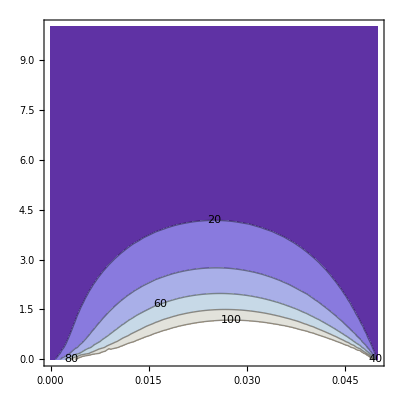

```mathematica
ContourPlot[Tt[5,x,t],{x,0,L},{t,0,10},ContourLabels->True]
```

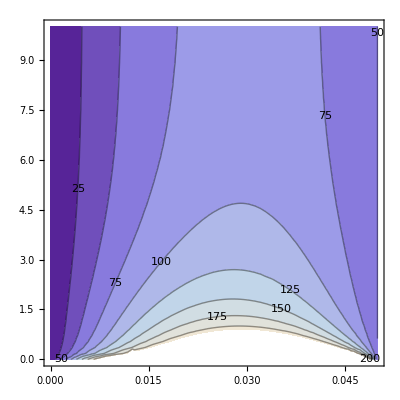

```mathematica
ContourPlot[T[5,x,t],{x,0,L},{t,0,10},ContourLabels->True]
```

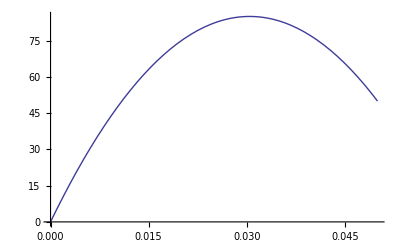

```mathematica
Plot[Ts[x],{x,0,L}]
```

```mathematica
D[Tt[1,x,t],x]
```

9066.67 ⅇ^(-0.473741 t) Cos[62.8319 x]

```mathematica
D[Tt[1,x,t],t]
```

-68.3611 ⅇ^(-0.473741 t) Sin[62.8319 x]

```mathematica
T[2,x,t]
```

-4533.33 x+229.167 x^2+144.3 ⅇ^(-0.473741 t) Sin[62.8319 x]+ⅇ^(-1.89496 t) (144.3 Sin[62.8319 x]-72.1502 Sin[125.664 x])

```mathematica
Tt[1,x,t]
```

144.3 ⅇ^(-0.473741 t) Sin[62.8319 x]

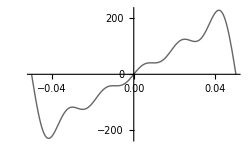

```mathematica
graphtwoF=Plot[fourierF[5,x],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

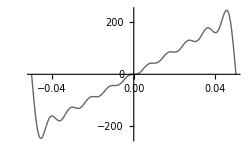

```mathematica
graphthreeF=Plot[fourierF[10,x],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

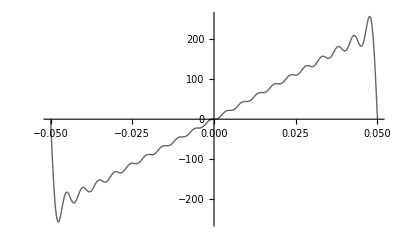

```mathematica
graphsixF=Plot[fourierF[20,x],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

```mathematica
Manipulate[Plot[Tt[n,x,t],{t,0,20},PlotRange->3],{n,1,20},{x,0,L}]
```

```mathematica
(* By manipulation of the above graph of Tt[x,t], it is observed that Tt has a maximum with respect to time at approxamately x=.0224.  The time it takes for the transient part to reach 2 at this position is approxamately 10 seconds.  *)
```

```mathematica
Solve[Tt[1,x,2.11]-2==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.000599519}}

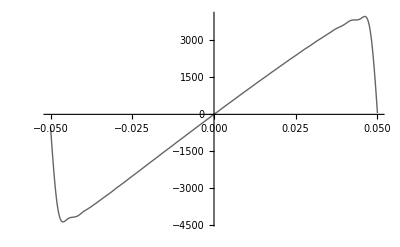

```mathematica
graphsixF=Plot[T[20,x,0],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

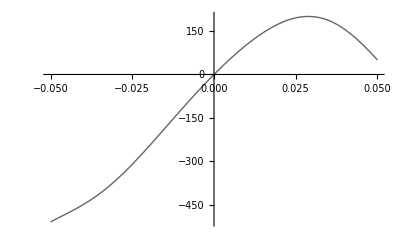

```mathematica
graphsixF=Plot[T[20,x,1],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

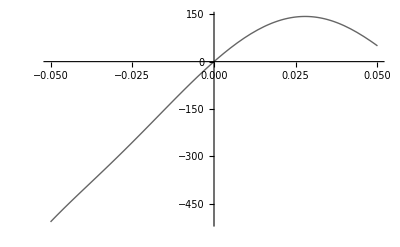

```mathematica
graphsixF=Plot[T[20,x,2],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

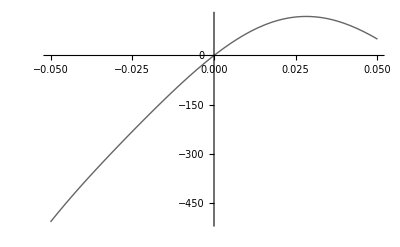

```mathematica
graphsixF=Plot[T[20,x,3],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

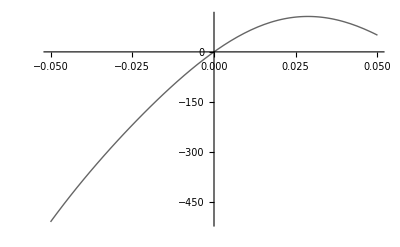

```mathematica
graphsixF=Plot[T[20,x,4],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

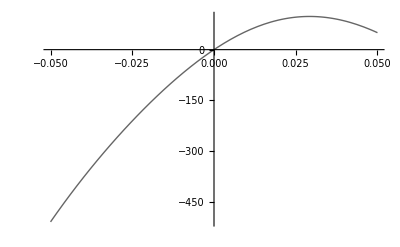

```mathematica
graphsixF=Plot[T[20,x,5],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

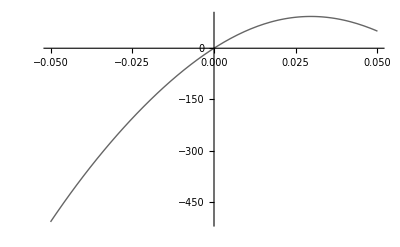

```mathematica
graphsixF=Plot[T[20,x,6],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

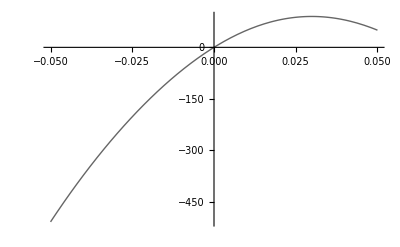

```mathematica
graphsixF=Plot[T[20,x,7],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

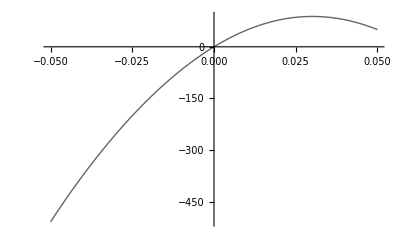

```mathematica
graphsixF=Plot[T[20,x,8],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

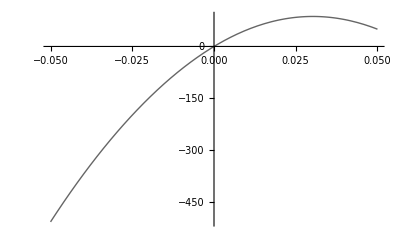

```mathematica
graphsixF=Plot[T[20,x,9],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```

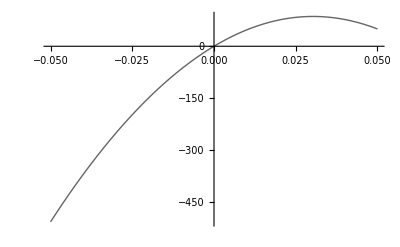

```mathematica
graphsixF=Plot[T[20,x,10],{x,-L,L},PlotStyle->GrayLevel[0.4]]
```